the rules of chess occupy 10 to the 5 pages in this language.

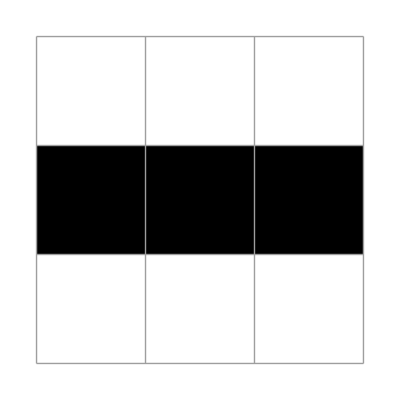
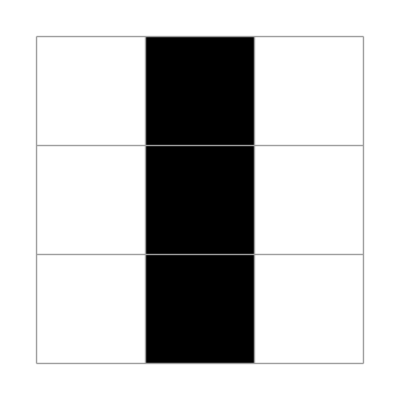

-Graphics-

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

```mathematica
Binomial[8,7]
```

8

```mathematica
Not/@Prepend[{1,2,3,4} ,xP]
```

{!xP,!1,!2,!3,!4}

## the second28

```mathematica
Clear[x];
lifeNeighbours={xNW,xN,xNE,xW,xE,xSW,xS,xSE};
listsSecond28stone=Subsets[lifeNeighbours,{2}];
listsSecond28=(Prepend[Prepend[# ,Not[x]],xP])&@((Not/@#)~Join~Complement[lifeNeighbours,#])&/@listsSecond28stone;
MessageDialog[listsSecond28//Length];
theSecond28=And@@Or@@@listsSecond28
```

(xP||!x||!xNW||!xN||xE||xNE||xS||xSE||xSW||xW)&&(xP||!x||!xNW||!xNE||xE||xN||xS||xSE||xSW||xW)&&(xP||!x||!xNW||!xW||xE||xN||xNE||xS||xSE||xSW)&&(xP||!x||!xNW||!xE||xN||xNE||xS||xSE||xSW||xW)&&(xP||!x||!xNW||!xSW||xE||xN||xNE||xS||xSE||xW)&&(xP||!x||!xNW||!xS||xE||xN||xNE||xSE||xSW||xW)&&(xP||!x||!xNW||!xSE||xE||xN||xNE||xS||xSW||xW)&&(xP||!x||!xN||!xNE||xE||xNW||xS||xSE||xSW||xW)&&(xP||!x||!xN||!xW||xE||xNE||xNW||xS||xSE||xSW)&&(xP||!x||!xN||!xE||xNE||xNW||xS||xSE||xSW||xW)&&(xP||!x||!xN||!xSW||xE||xNE||xNW||xS||xSE||xW)&&(xP||!x||!xN||!xS||xE||xNE||xNW||xSE||xSW||xW)&&(xP||!x||!xN||!xSE||xE||xNE||xNW||xS||xSW||xW)&&(xP||!x||!xNE||!xW||xE||xN||xNW||xS||xSE||xSW)&&(xP||!x||!xNE||!xE||xN||xNW||xS||xSE||xSW||xW)&&(xP||!x||!xNE||!xSW||xE||xN||xNW||xS||xSE||xW)&&(xP||!x||!xNE||!xS||xE||xN||xNW||xSE||xSW||xW)&&(xP||!x||!xNE||!xSE||xE||xN||xNW||xS||xSW||xW)&&(xP||!x||!xW||!xE||xN||xNE||xNW||xS||xSE||xSW)&&(xP||!x||!xW||!xSW||xE||xN||xNE||xNW||xS||xSE)&&(xP||!x||!xW||!xS||xE||xN||xNE||xNW||xSE||xSW)&&(xP||!x||!xW||!xSE||xE||xN||xNE||xNW||xS||xSW)&&(xP||!x||!xE||!xSW||xN||xNE||xNW||xS||xSE||xW)&&(xP||!x||!xE||!xS||xN||xNE||xNW||xSE||xSW||xW)&&(xP||!x||!xE||!xSE||xN||xNE||xNW||xS||xSW||xW)&&(xP||!x||!xSW||!xS||xE||xN||xNE||xNW||xSE||xW)&&(xP||!x||!xSW||!xSE||xE||xN||xNE||xNW||xS||xW)&&(xP||!x||!xS||!xSE||xE||xN||xNE||xNW||xSW||xW)